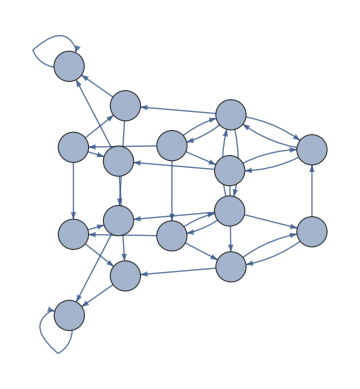

{{{0→0,1→0,2→0,3→0,4→0,5→0,6→0,7→0,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0},d<p&&d+r<1+d p},{{0→0,1→1,2→0,3→0,4→0,5→3,6→0,7→0,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0},d<p&&1+d p<d+r&&(1+d) r<1+d p},{{0→0,1→0,2→0,3→0,4→0,5→0,6→9,7→8,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0},d<p+d p&&d+r<1+d p&&d>p},{{0→0,1→1,2→0,3→0,4→0,5→3,6→9,7→8,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0},1+d p<d+r&&d r<p&&d>p&&1+d p>r+d r},{{0→0,1→0,2→0,3→0,4→13,5→12,6→9,7→8,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0},d+r<1+d p&&d>p+d p},{{0→0,1→1,2→0,3→0,4→13,5→12,6→9,7→8,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0},r+d r<1&&d+r>1+d p},{{0→0,1→1,2→0,3→0,4→0,5→15,6→9,7→8,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0},1+d p>r+d r&&p+d p>d&&d r>p},{{0→0,1→1,2→0,3→0,4→13,5→15,6→9,7→8,8→0,9→0,10→0,11→0,12→0,13→0,14→0,15→0},r+d r<1+d p&&d>p+d p&&d+r>1+d p&&(p+r>1||r+d r>1)},{{0→0,1→1,2→0,3→0,4→0,5→3,6→0,7→0,8→0,9→9,10→0,11→0,12→0,13→11,14→0,15→0},d<p&&1+d p<r+d r},{{0→0,1→1,2→0,3→0,4→0,5→3,6→9,7→8,8→0,9→9,10→0,11→0,12→0,13→11,14→0,15→0},1+d p<r+d r&&d r<p&&d>p},{{0→0,1→1,2→0,3→0,4→0,5→15,6→9,7→8,8→0,9→9,10→0,11→0,12→0,13→11,14→0,15→0},d<p+d p&&d r>p&&(1+d) r>1+d p},{{0→0,1→1,2→0,3→0,4→13,5→15,6→9,7→8,8→0,9→9,10→0,11→0,12→0,13→11,14→0,15→0},1+d p<r+d r&&p+d p<d}}

```mathematica
counter[i_,t_,r_,p_,s_,d_]:=
Module[{input = i},
assumptions = {
               If[input[[1]]==0, Q2000>Q2001, Q2000<Q2001],
               If[input[[2]]==0, Q2010>Q2011, Q2010<Q2011],
               If[input[[3]]==0, Q2100>Q2101, Q2100<Q2101],
               If[input[[4]]==0, Q2110>Q2111, Q2110<Q2111]
};
Assuming[assumptions,
{
q1=Simplify[Boole[Q2000>Q2001](p+d*Max[Q1000,Q1001])+Boole[Q2000<Q2001](t+d*Max[Q1010,Q1011])],q2=Simplify[Boole[Q2000>Q2001](s+d*Max[Q1100,Q1101])+Boole[Q2000<Q2001](r+d*Max[Q1110,Q1111])],q3=Simplify[Boole[Q2100>Q2101](p+d*Max[Q1000,Q1001])+Boole[Q2100<Q2101](t+d*Max[Q1010,Q1011])],q4=Simplify[Boole[Q2100>Q2101](s+d*Max[Q1100,Q1101])+Boole[Q2100<Q2101](r+d*Max[Q1110,Q1111])],q5=Simplify[Boole[Q2010>Q2011](p+d*Max[Q1000,Q1001])+Boole[Q2010<Q2011](t+d*Max[Q1010,Q1011])],q6=Simplify[Boole[Q2010>Q2011](s+d*Max[Q1100,Q1101])+Boole[Q2010<Q2011](r+d*Max[Q1110,Q1111])],q7=Simplify[Boole[Q2110>Q2111](p+d*Max[Q1000,Q1001])+Boole[Q2110<Q2111](t+d*Max[Q1010,Q1011])],q8=Simplify[Boole[Q2110>Q2111](s+d*Max[Q1100,Q1101])+Boole[Q2110<Q2111](r+d*Max[Q1110,Q1111])]
}];

sol=Solve[{q1==Q1000, q2==Q1001, q3==Q1010, q4==Q1011, q5==Q1100, q6==Q1101, q7==Q1110, q8==Q1111},
                        {Q1000, Q1001, Q1010, Q1011, Q1100, Q1101, Q1110, Q1111}];
output = {0,0,0,0};
output[[1]]=Boole[sol[[1]][[1]][[2]] < sol[[1]][[2]][[2]]];
output[[2]]=Boole[sol[[1]][[3]][[2]] < sol[[1]][[4]][[2]]];
output[[3]]=Boole[sol[[1]][[5]][[2]] < sol[[1]][[6]][[2]]];
output[[4]]=Boole[sol[[1]][[7]][[2]] < sol[[1]][[8]][[2]]];
output
];

(*All 16 strategies*)
strats = {};
Do[AppendTo[strats, Join[ConstantArray[0,4-Length[IntegerDigits[i,2]]],IntegerDigits[i,2]]],{i,0,15}];

(*Calculate the best responses*)
(*Change the values here*)
bestresps = {};
Do[AppendTo[bestresps, counter[strats[[i]],4,3,2,1,9/10]],{i,1,16}]
bestresps;


differences = ConstantArray[{},16];
Do[Do[Which[bestresps[[i]][[j]] != strats[[i]][[j]] ,If[strats[[i]][[j]]==0,AppendTo[differences[[i]],ReplacePart[strats[[i]],j->1]], 
														AppendTo[differences[[i]],ReplacePart[strats[[i]],j->0]]
],bestresps[[i]]==strats[[i]]&& j == 1, AppendTo[differences[[i]], strats[[i]]]],{j,1,4}],{i,1,16}]


(*Make the small graph*)
edges = {};
Do[Do[AppendTo[edges, FromDigits[strats[[i]],2]+1->FromDigits[differences[[i]][[j]],2] + 1],{j,1,Length[differences[[i]]]}],{i,1,16}];
Graph[edges, VertexLabels->Placed[Automatic,Center],VertexSize->.75, ImageSize->Medium]



smalladistr[graph_] :=
Module[{g=graph},
(*All 256 strategy pairs*)
inputlist = {};
Do[AppendTo[inputlist, Join[ConstantArray[0,8-Length[IntegerDigits[i,2]]],IntegerDigits[i,2]]],{i,0,255}];

bestresps = {};
Do[bestresps = AppendTo[bestresps,toBin[g[[i]][[2]],4]],{i,1,Length[g]}];

(*Find the best responses to the pairs*)
counterstrats = {};
Do[
p1 =FromDigits[inputlist[[i]][[1;;4]],2] + 1 ;
p2 = FromDigits[inputlist[[i]][[5;;8]],2] + 1 ;
AppendTo[counterstrats,Join[bestresps[[p2]],bestresps[[p1]]]];
,{i,1,256}];

differences2= ConstantArray[{},256];
Do[Do[Which[counterstrats[[i]][[j]] != inputlist[[i]][[j]] ,If[inputlist[[i]][[j]]==0,AppendTo[differences2[[i]],ReplacePart[inputlist[[i]],j->1]], 
														AppendTo[differences2[[i]],ReplacePart[inputlist[[i]],j->0]]
],counterstrats[[i]]==inputlist[[i]]&& j == 1, AppendTo[differences2[[i]], inputlist[[i]]]],{j,1,8}],{i,1,256}];

(*Uniform*)
transitionmatrix = ConstantArray[ConstantArray[0,256],256];
Do[Do[transitionmatrix[[i]][[FromDigits[differences2[[i]][[j]],2]+1]] = 1/ Length[differences2[[i]]],{j,1,Length[differences2[[i]]]}],{i,1,256}];


P = DiscreteMarkovProcess[ConstantArray[1/256,256],transitionmatrix];

PDF[StationaryDistribution[P],Table[i,{i,1,256}]]
];
(*Make the large graph*)
(*edges = {};
Do[Do[AppendTo[edges, FromDigits[inputlist[[i]],2]+1->FromDigits[differences2[[i]][[j]],2] + 1],{j,1,Length[differences2[[i]]]}],{i,1,256}];


GraphPlot[edges, VertexLabels->Automatic, DirectedEdges->True, ImageSize->Full]*)
Graphs
collist;
distra = Table[smalladistr[Graphs[[i]][[1]]],{i,1,Length[Graphs]}];
```

```mathematica
percents = Table[Table[N[Sum[distra[[j]][[k]]*Boole[MemberQ[collist[[i]],k-1]],{k,1,256}]],{j,1,Length[Graphs[[All,1]]]}],{i,1,Length[collist]}]
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.0801841,0.0938113,0.110336,0.153387},{1.,1.,1.,1.,1.,1.,1.,1.,0.919816,0.906189,0.889664,0.846613}}

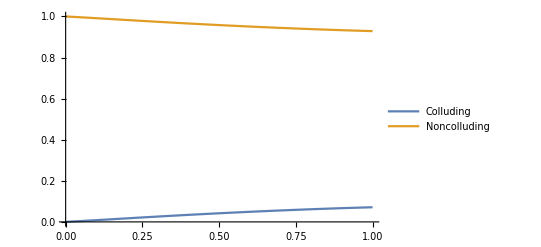

/home/lars/Documents/Year 3/Bachelor project/Informatica/Mathematica/Collusion Prisoner a.png

```mathematica
colarea[delta_,type_]:=Sum[percents[[type]][[i]]*Area[ImplicitRegion[todraw[[i]]/.{d->delta,inside[[1]]->x,inside[[2]]->y},{x,y}]],{i,1,Length[todraw]}]

plot = Plot[{colarea[d,1]*2,colarea[d,2]*2},{d,0,1},PlotLegends->{"Colluding","Noncolluding"},PlotRange->{0,1}]
Export["/home/lars/Documents/Year 3/Bachelor project/Informatica/Mathematica/Collusion Prisoner a.png",plot]
```